# クラスタリング評価指標 SI

## Program

```mathematica
subMat[mat_,lw_,up_]:=Transpose[Transpose[mat[[lw;;up]]][[lw;;up]]]
```

```mathematica
subMat[mat_,sel_List]:=Transpose[Transpose[mat[[sel]]][[sel]]]
```

```mathematica
subMat[mat_,selL_List,selC_List]:=Transpose[Transpose[mat[[selL]]][[selC]]]
```

```mathematica
averageDist[l_]:=Mean[Map[EuclideanDistance[#,Mean[l]]&,l]]
```

```mathematica
WCSPowerWeighted[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]
```

```mathematica
WCSPowerWeighted[memOfCls_List,radOfCls_List,meanRadTotal_]:=Length[memOfCls]*Tr[memOfCls^(radOfCls/meanRadTotal),Times]
```

指標SI (pi): 距離をベースとするクラスタリング評価指標

SI(piS) = K ∏_(i=1)^K n[i]^(d[i]/D)

(SI(piG) = K (∏_(i=1)^K n[i]^(d[i]/D)))^(1/K)

K :  クラスタ数; 
n[i] : クラスタiのメンバー数; 
d[i] : クラスタiのdispersion (半径などの代表距離); 
D : 全サンプルにおけるdispersion (半径などの代表距離).
値が小さいほど適正

```mathematica
piS[mat_,cls_]:=Module[{classes},classes=Map[mat[[#]]&,cls];
WCSPowerWeighted[classes]]
```

```mathematica
piG[mat_,cls_]:=Module[{numMem,numCL,numsCLMem,totalCenter,totalRmean,classes,centers,rs},numMem=Length[mat];
numCL=Length[cls];
numsCLMem=Map[Length,cls];
totalCenter=Mean[mat];
totalRmean=Mean[Map[EuclideanDistance[#,totalCenter]&,mat]];
classes=Map[mat[[#]]&,cls];
centers=Map[Mean,classes];
rs=Table[Mean[Map[EuclideanDistance[#,centers[[n]]]&,classes[[n]]]],{n,numCL}]/totalRmean;
numCL*(Tr[Table[numsCLMem[[n]]^rs[[n]],{n,numCL}],Times])^(1/numCL)]
```

指標SI (piDM): 距離行列をベースとするクラスタリング評価指標

SI(piDMS) = K ∏_(i=1)^K n[i]^(d[i]/D)

(SI(piDMG) = K (∏_(i=1)^K n[i]^(d[i]/D)))^(1/K)

K :  クラスタ数; 
n[i] : クラスタiのメンバー数; 
d[i] : クラスタiの距離行列の平均値; 
D : 全サンプルにおける距離行列の平均値.
値が小さいほど適正

```mathematica
piDMG[dmat_(*distance matrix*),cls_]:=Module[{k,meanS,nums,simCls},k=Length[cls];
meanS=Mean[Flatten[dmat]];
nums=Map[Length,cls];
simCls=Map[Mean[Flatten[subMat[dmat,#]]]/meanS&,cls];
k Inner[Power,nums,simCls,Times]^(1/k)];
```

指標SIs (piSIM): 類似度をベースとするクラスタリング評価指標

SIs(piSIM) = K ∏_(i=1)^K n[i]^(S/s[i])

(SIs(piSIMG) = K (∏_(i=1)^K n[i]^(S/s[i])))^(1/K)

K :  クラスタ数; 
n[i] : クラスタiのメンバー数; 
S : 類似度行列全体の平均;
s[i] : クラスタ内メンバーの類似度の平均.
値が小さいほど適正

```mathematica
piSIM[smat_(*similarity matrix*),cls_]:=Module[{k,meanS,nums,simCls},k=Length[cls];
meanS=Mean[Flatten[smat]];
nums=Map[Length,cls];
simCls=Map[meanS/Mean[Flatten[subMat[smat,#]]]&,cls];
k Inner[Power,nums,simCls,Times]];
```

```mathematica
piSIMG[smat_(*similarity matrix*),cls_]:=Module[{k,meanS,nums,simCls},k=Length[cls];
meanS=Mean[Flatten[smat]];
nums=Map[Length,cls];
simCls=Map[meanS/Mean[Flatten[subMat[smat,#]]]&,cls];
k Inner[Power,nums,simCls,Times]^(1/k)];
```

```mathematica
seqSim[s1_,s2_]:=Inner[Times,Normalize[s1],Normalize[s2],Plus]
```

最新プログラム: https://github.com/kouamano/MATH_SCRIPT/tree/master/SCRIPTS

## 使い方

piS

対象データとそのクラス分けを与える。クラスタ半径に基づく。

```mathematica
testdata={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

{{1番目のスペクトル},{2番目のスペクトル,3番目のスペクトル}} と分けてみる:

```mathematica
piS[testdata,{{1},{2,3}}]//N
```

3.64527

piSIM

「対象データの類似度行列」とそのクラス分けを与える。スペクトルの内積に基づく。

まず類似度行列を求める

```mathematica
sims=Outer[seqSim,testdata,testdata,1]
```

{{1,0,0},{0,1,0},{0,0,1}}

{{1 番目のスペクトル}, {2 番目のスペクトル, 3 番目のスペクトル}} と分けてみる :

```mathematica
piSIM[sims,{{1},{2,3}}]//N
```

3.1748

全て違うグループに分ける:

```mathematica
piSIM[sims,{{1},{2},{3}}]
```

3

全て同じグループに属させる:

```mathematica
piSIM[sims,{{1,2,3}}]
```

3

# SIを利用したクラスターツリーのビルドアップ全探索による最適分類

## Program(クラスカル法によるツリーのビルド)

```mathematica
kruskalFirstGr[li_]:=Table[n,{n,Length[li]}]
```

```mathematica
findFirstMinPos[dmat_]:=Position[dmat,Min[dmat],2][[1]]
```

```mathematica
firstKruskalDmat[dmat_]:=ReplacePart[dmat,{x_,y_}/;y<=x->Infinity]
```

```mathematica
dmatRewrite[dmat_,pos_]:=ReplacePart[dmat,pos->Infinity]
```

```mathematica
classRewrite[classList_,pos_]:=Module[{targetPos,minId,reprls},
targetPos=Flatten[{Position[classList,classList[[pos[[1]]]]],Position[classList,classList[[pos[[2]]]]]}];
minId=Min[{classList[[pos[[1]]]],classList[[pos[[2]]]]}];
reprls=Map[#->minId&,targetPos];
ReplacePart[classList,reprls]
]
```

```mathematica
nextKruskal[{dmat_,classList_}]:=Module[{outdmat,outClassList,minpos},
minpos=findFirstMinPos[dmat];
outdmat=dmatRewrite[dmat,minpos];
outClassList=classRewrite[classList,minpos];
{outdmat,outClassList}
]
```

```mathematica
nextKruskalEdge[{dmat_,classList_,mstEdge_}]:=Module[{outdmat,outClassList,minpos,outMSTEdge},
minpos=findFirstMinPos[dmat];
outdmat=dmatRewrite[dmat,minpos];
outClassList=classRewrite[classList,minpos];
If[classList[[minpos[[1]]]]!=classList[[minpos[[2]]]],outMSTEdge=Append[mstEdge,minpos],outMSTEdge=mstEdge];
{outdmat,outClassList,outMSTEdge}
]
```

```mathematica
kruskalBuild[data_]:=Module[{len,dmat,dmat1,li1},
len=Length[data];
dmat=Outer[EuclideanDistance,data,data,1];
dmat1=firstKruskalDmat[dmat];
li1=kruskalFirstGr[data];
NestList[nextKruskal,{dmat1,li1},(len*len-len)/2]
]
```

```mathematica
kruskalBuild[data_,n_]:=Module[{len,dmat,dmat1,li1},
len=Length[data];
dmat=Outer[EuclideanDistance,data,data,1];
dmat1=firstKruskalDmat[dmat];
li1=kruskalFirstGr[data];
NestList[nextKruskal,{dmat1,li1},n]
]
```

```mathematica
kruskalEdgeBuild[data_]:=Module[{len,dmat,dmat1,li1},
len=Length[data];
dmat=Outer[EuclideanDistance,data,data,1];
dmat1=firstKruskalDmat[dmat];
li1=kruskalFirstGr[data];
NestList[nextKruskalEdge,{dmat1,li1,{}},(len*len-len)/2]
]
```

```mathematica
kruskalEdgeWhileBuild[data_]:=Module[{len,dmat,dmat1,li1},
len=Length[data];
dmat=Outer[EuclideanDistance,data,data,1];
dmat1=firstKruskalDmat[dmat];
li1=kruskalFirstGr[data];
NestWhileList[nextKruskalEdge,{dmat1,li1,{}},Length[Union[#[[2]]]]≥2& ]
]
```

```mathematica
kruskalEdgeBuild[data_,n_]:=Module[{len,dmat,dmat1,li1},
len=Length[data];
dmat=Outer[EuclideanDistance,data,data,1];
dmat1=firstKruskalDmat[dmat];
li1=kruskalFirstGr[data];
NestList[nextKruskalEdge,{dmat1,li1,{}},n]
]
```

```mathematica
createMST[dmat_,edgeList_]:=Map[Flatten[{#,dmat[[#[[1]],#[[2]]]]}]&,edgeList]
```

最新プログラム: https://github.com/kouamano/MATH_SCRIPT/tree/master/SCRIPTS

## Program(ツリーから対象構造の抽出)

```mathematica
ContainsAny[l1_,l2_]:=(Intersection[l1,l2]≠{})
```

```mathematica
makeClusterByGr[li_]:=Module[{classes},
classes=Union[li];
Map[Flatten[Position[li,#]]&,classes]
]
```

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]≤1]:={}
```

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]==2]:=Module[{mstEd},
mstEd=Map[Sort[{#[[1]],#[[2]]}]&,mst];
mst[[Flatten[Position[mstEd,Sort[cl]]]]]
]
```

```mathematica
extractEdgeGrFromCl[mst_,cl_/;Length[cl]≥3]:=Module[{mstEd,startEd,endEd,startContPos,endContPos},
mstEd=Map[Sort[{#[[1]],#[[2]]}]&,mst];
startEd=Map[#[[1]]&,mst];
endEd=Map[#[[2]]&,mst];
startContPos=Position[Map[ContainsAny[cl,{#}]&,startEd],True];
endContPos=Position[Map[ContainsAny[cl,{#}]&,endEd],True];
mst[[Flatten[Intersection[startContPos,endContPos]]]]
]
```

```mathematica
makeEdgeGrFromCluster[mst_,cl_]:=Map[extractEdgeGrFromCl[mst,#]&,cl]
```

```mathematica
radiusOfAllClSamples[cl_List]:=Module[{center},center=Mean[Flatten[cl,1]];
Mean[Map[EuclideanDistance[center,#]&,Flatten[cl,1]]]]
```

```mathematica
takeVecByID[mat_,li_]:=Map[mat[[#]]&,li];
```

```mathematica
centerOfAllClSamples[cl_List]:=Mean[Flatten[cl,1]]
```

```mathematica
centerOfEachClusters[cl_List]:=Map[Mean[#]&,cl]
```

```mathematica
distancesFromEachClToCenter[cl_List]:=Module[{totalcenter,eachclcenter},totalcenter=centerOfAllClSamples[cl];
eachclcenter=centerOfEachClusters[cl];
Map[EuclideanDistance[totalcenter,#]&,eachclcenter]]
```

最新プログラム: https://github.com/kouamano/MATH_SCRIPT/tree/master/SCRIPTS

## 使い方

```mathematica
data={{1,2},{3,4},{3,5},{7,8},{8,9},{6,9}}
```

{{1,2},{3,4},{3,5},{7,8},{8,9},{6,9}}

```mathematica
simd=Outer[seqSim,data,data,1]
```

{{1,11/(5 √5),√(10/17)+3/(√170),23/(√565),26/(5 √29),8/(√65)},{11/(5 √5),1,2 √(2/17)+9/(5 √34),53/(5 √113),12/(√145),18/(5 √13)},{√(10/17)+3/(√170),2 √(2/17)+9/(5 √34),1,20 √(2/1921)+21/(√3842),12 √(2/2465)+9 √(5/986),3 √(2/221)+15/(√442)},{23/(√565),53/(5 √113),20 √(2/1921)+21/(√3842),1,128/(√16385),38/(√1469)},{26/(5 √29),12/(√145),12 √(2/2465)+9 √(5/986),128/(√16385),1,43/(√1885)},{8/(√65),18/(5 √13),3 √(2/221)+15/(√442),38/(√1469),43/(√1885),1}}

```mathematica
keb=kruskalEdgeWhileBuild[data]
```

{{{{∞,2 √2,√13,6 √2,7 √2,√74},{∞,∞,1,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,√2,√2},{∞,∞,∞,∞,∞,2},{∞,∞,∞,∞,∞,∞}},{1,2,3,4,5,6},{}},{{{∞,2 √2,√13,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,√2,√2},{∞,∞,∞,∞,∞,2},{∞,∞,∞,∞,∞,∞}},{1,2,2,4,5,6},{{2,3}}},{{{∞,2 √2,√13,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,∞,√2},{∞,∞,∞,∞,∞,2},{∞,∞,∞,∞,∞,∞}},{1,2,2,4,4,6},{{2,3},{4,5}}},{{{∞,2 √2,√13,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,2},{∞,∞,∞,∞,∞,∞}},{1,2,2,4,4,4},{{2,3},{4,5},{4,6}}},{{{∞,2 √2,√13,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞}},{1,2,2,4,4,4},{{2,3},{4,5},{4,6}}},{{{∞,∞,√13,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞}},{1,1,1,4,4,4},{{2,3},{4,5},{4,6},{1,2}}},{{{∞,∞,∞,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,5,√41,5},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞}},{1,1,1,4,4,4},{{2,3},{4,5},{4,6},{1,2}}},{{{∞,∞,∞,6 √2,7 √2,√74},{∞,∞,∞,4 √2,5 √2,√34},{∞,∞,∞,∞,√41,5},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞}},{1,1,1,1,1,1},{{2,3},{4,5},{4,6},{1,2},{3,4}}}}

グループIDリストの抽出

```mathematica
idGrs=Union[Map[#[[2]]&,keb]]
```

{{1,1,1,1,1,1},{1,1,1,4,4,4},{1,2,2,4,4,4},{1,2,2,4,4,6},{1,2,2,4,5,6},{1,2,3,4,5,6}}

MSTを生成

```mathematica
mstedge=keb[[-1]][[3]]
```

{{2,3},{4,5},{4,6},{1,2},{3,4}}

```mathematica
(dmat=Outer[EuclideanDistance,data,data,1])//TableForm
```

0 | 2 √2 | √13 | 6 √2 | 7 √2 | √74
2 √2 | 0 | 1 | 4 √2 | 5 √2 | √34
√13 | 1 | 0 | 5 | √41 | 5
6 √2 | 4 √2 | 5 | 0 | √2 | √2
7 √2 | 5 √2 | √41 | √2 | 0 | 2
√74 | √34 | 5 | √2 | 2 | 0

```mathematica
mst=createMST[dmat,mstedge]
```

{{2,3,1},{4,5,√2},{4,6,√2},{1,2,2 √2},{3,4,5}}

グループIDよりクラスターを生成

```mathematica
cls=Map[makeClusterByGr,idGrs]
```

{{{1,2,3,4,5,6}},{{1,2,3},{4,5,6}},{{1},{2,3},{4,5,6}},{{1},{2,3},{4,5},{6}},{{1},{2,3},{4},{5},{6}},{{1},{2},{3},{4},{5},{6}}}

CVI評価:

piS

```mathematica
t=Table[piS[data,cls[[n]]],{n,Length[data]}]//N
```

{6.,4.25563,4.44537,5.09238,5.52592,6.}

```mathematica
Position[t,Min[t]]
```

{{2}}

cls[[2]] が適正

piG

```mathematica
t=Table[piG[data,cls[[n]]],{n,Length[data]}]//N
```

{6.,2.91741,3.42019,4.24889,5.10102,6.}

```mathematica
Position[t,Min[t]]
```

{{2}}

cls[[2]] が適正

piSIM

```mathematica
t2=Table[piSIM[simd,cls[[n]]],{n,Length[data]}]//N
```

{6.,17.8373,17.828,15.8341,9.95708,6.}

```mathematica
Position[t2,Min[t2]]
```

{{1},{6}}

ベースラインが小さすぎる

piSIMG

```mathematica
t3=Table[piSIMG[simd,cls[[n]]],{n,Length[data]}]//N
```

{6.,5.97282,5.43394,5.64214,5.73855,6.}

```mathematica
Position[t3,Min[t3]]
```

{{3}}

cls[[3]] が適正

# 応用:カロテノイドの分類高精度化(1) ~クラスカル法~

## Data

```mathematica
SetDirectory["/Users/amanokou/TEXT/Cluster-Validity/SCCJ/carotenoides"]
```

/Users/amanokou/Documents/Cluster-Validity/SCCJ/carotenoides

```mathematica
(*SetDirectory["/Users/kouamano/TEXT/Cluster-Validity/SCCJ/carotenoides"]*)
```

```mathematica
xls=Import["carotenoids.xlsx"];
```

```mathematica
colnames=xls[[1,5]]
```

{,,,,UV,Excitation,Orbital Energy,HOMO ,LUMO ,HOMO-LUMO Gap,IR,Vib. Freq.,S0-T1
Splitting,IE,EA}

```mathematica
colnamesT=colnames[[5;;-1]]
```

{UV,Excitation,Orbital Energy,HOMO ,LUMO ,HOMO-LUMO Gap,IR,Vib. Freq.,S0-T1
Splitting,IE,EA}

```mathematica
(caroteData=xls[[1,6;;-1]])//Length
```

30

```mathematica
(caroteDataT=Map[Normalize[#[[5;;-1]]]&,caroteData])//Dimensions
```

{30,11}

```mathematica
caroteDataID=Map[#[[2]]&,caroteData]
```

{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,c01,c02,c03,c04,c05,c06,c07,c08,c09}

```mathematica
caroteDataName=Map[#[[3]]&,caroteData]
```

{Bacterioruberin,Monoanhydrobacterioruberin,Bisanhydrobacterioruberin,Spirilloxanthin,Rhodopin,Rhodopinal,Chlorobactene,Hydroxychlorobactene,Myxol,Okadaxanthin,Diatoxanthin,Mytiloxanthin,Isomytiloxanthin,Alloxanthin,Amarouciaxanthin A,Peridininol,Pectenol,Pectenolone,Mactraxanthin,Halocynthiaxanthin,Fucoxanthinol,Salmoxanthin,Tunaxanthin,Lutein A,Lutein B,Fritschiellaxanthin,a-doradexanthin,b-doradexanthin,Astaxanthin,Zeaxanthin}

## 評価

```mathematica
ceb=kruskalEdgeWhileBuild[caroteDataT]
```

{1}
 |  |  |  |

```mathematica
(idcGrs=Union[Map[#[[2]]&,ceb]])//Short
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},«28»,{1,2,3,«25»,29,30}}

```mathematica
cmstedge=ceb[[-1]][[3]]
```

{{7,8},{27,28},{1,2},{26,27},{23,25},{11,27},{24,25},{3,4},{10,25},{14,28},{20,21},{17,26},{11,30},{2,3},{25,30},{5,9},{15,20},{16,21},{18,29},{20,26},{8,11},{14,18},{5,7},{22,23},{19,24},{3,9},{4,6},{12,15},{13,21}}

```mathematica
(cdmat=Outer[EuclideanDistance,caroteDataT,caroteDataT,1])//TableForm
```

0. | 0.0219775 | 0.0638431 | 0.0698849 | 0.135516 | 0.175364 | 0.186387 | 0.18963 | 0.115219 | 0.307131 | 0.254538 | 0.318031 | 0.303526 | 0.247611 | 0.353664 | 0.375916 | 0.263037 | 0.198914 | 0.350064 | 0.322191 | 0.348099 | 0.31585 | 0.315112 | 0.30271 | 0.29595 | 0.271819 | 0.258508 | 0.246556 | 0.235108 | 0.264351
0.0219775 | 0. | 0.0440391 | 0.05632 | 0.130078 | 0.163904 | 0.186666 | 0.190275 | 0.107763 | 0.308866 | 0.25448 | 0.316786 | 0.297809 | 0.245547 | 0.352487 | 0.370498 | 0.261627 | 0.193201 | 0.345828 | 0.319225 | 0.34425 | 0.317171 | 0.315087 | 0.30189 | 0.296443 | 0.270831 | 0.258153 | 0.245342 | 0.226239 | 0.264804
0.0638431 | 0.0440391 | 0. | 0.0287935 | 0.130086 | 0.134839 | 0.190352 | 0.194791 | 0.101443 | 0.314213 | 0.254157 | 0.307831 | 0.278566 | 0.239669 | 0.34431 | 0.357322 | 0.258375 | 0.181305 | 0.340709 | 0.309677 | 0.332499 | 0.320845 | 0.318723 | 0.303596 | 0.30118 | 0.266817 | 0.256022 | 0.24158 | 0.211666 | 0.267643
0.0698849 | 0.05632 | 0.0287935 | 0. | 0.136685 | 0.122695 | 0.191523 | 0.196152 | 0.106418 | 0.315883 | 0.252771 | 0.300098 | 0.267533 | 0.236034 | 0.337835 | 0.35575 | 0.258251 | 0.178609 | 0.343306 | 0.305988 | 0.328611 | 0.322958 | 0.323064 | 0.306892 | 0.30518 | 0.264196 | 0.253676 | 0.239173 | 0.214107 | 0.269421
0.135516 | 0.130078 | 0.130086 | 0.136685 | 0. | 0.187443 | 0.0754941 | 0.0791474 | 0.050562 | 0.190756 | 0.137272 | 0.230897 | 0.210067 | 0.13121 | 0.245333 | 0.258778 | 0.149576 | 0.0878752 | 0.218585 | 0.20727 | 0.233663 | 0.209896 | 0.194823 | 0.178447 | 0.176667 | 0.157881 | 0.144607 | 0.131852 | 0.113927 | 0.147562
0.175364 | 0.163904 | 0.134839 | 0.122695 | 0.187443 | 0. | 0.232953 | 0.237872 | 0.172611 | 0.341549 | 0.276967 | 0.296319 | 0.229414 | 0.256073 | 0.326419 | 0.334695 | 0.281169 | 0.191894 | 0.341962 | 0.304097 | 0.316194 | 0.350519 | 0.348199 | 0.32786 | 0.332873 | 0.278141 | 0.272554 | 0.25736 | 0.213686 | 0.297353
0.186387 | 0.186666 | 0.190352 | 0.191523 | 0.0754941 | 0.232953 | 0. | 0.00623073 | 0.0986924 | 0.126059 | 0.071849 | 0.188083 | 0.18985 | 0.0801933 | 0.188846 | 0.218212 | 0.0871792 | 0.0791121 | 0.18416 | 0.154721 | 0.186914 | 0.14761 | 0.137135 | 0.123261 | 0.117495 | 0.0978532 | 0.0818321 | 0.072258 | 0.118695 | 0.0813473
0.18963 | 0.190275 | 0.194791 | 0.196152 | 0.0791474 | 0.237872 | 0.00623073 | 0. | 0.102641 | 0.12154 | 0.0694452 | 0.187503 | 0.191818 | 0.0807208 | 0.187443 | 0.217103 | 0.0851089 | 0.0825223 | 0.181879 | 0.153514 | 0.1858 | 0.143192 | 0.132583 | 0.119248 | 0.112838 | 0.0960064 | 0.0799325 | 0.0712811 | 0.120258 | 0.0770874
0.115219 | 0.107763 | 0.101443 | 0.106418 | 0.050562 | 0.172611 | 0.0986924 | 0.102641 | 0. | 0.219204 | 0.159284 | 0.23064 | 0.213252 | 0.148865 | 0.256002 | 0.269925 | 0.16138 | 0.0966873 | 0.250073 | 0.21725 | 0.242906 | 0.225833 | 0.221783 | 0.206702 | 0.205093 | 0.17231 | 0.162161 | 0.147686 | 0.130548 | 0.170934
0.307131 | 0.308866 | 0.314213 | 0.315883 | 0.190756 | 0.341549 | 0.126059 | 0.12154 | 0.219204 | 0. | 0.075966 | 0.190591 | 0.218675 | 0.11364 | 0.144619 | 0.177306 | 0.0904736 | 0.166301 | 0.121071 | 0.125302 | 0.153438 | 0.083653 | 0.041564 | 0.0440848 | 0.0315948 | 0.0937037 | 0.088583 | 0.100519 | 0.173572 | 0.0532113
0.254538 | 0.25448 | 0.254157 | 0.252771 | 0.137272 | 0.276967 | 0.071849 | 0.0694452 | 0.159284 | 0.075966 | 0. | 0.157387 | 0.163813 | 0.0421386 | 0.129423 | 0.169669 | 0.0467887 | 0.0967186 | 0.136769 | 0.0976458 | 0.131627 | 0.108828 | 0.0925699 | 0.0764053 | 0.0771526 | 0.0412264 | 0.0255805 | 0.0304087 | 0.120749 | 0.0407273
0.318031 | 0.316786 | 0.307831 | 0.300098 | 0.230897 | 0.296319 | 0.188083 | 0.187503 | 0.23064 | 0.190591 | 0.157387 | 0. | 0.135309 | 0.152624 | 0.123801 | 0.169245 | 0.143409 | 0.159295 | 0.214037 | 0.126055 | 0.137341 | 0.148879 | 0.199257 | 0.191845 | 0.197119 | 0.130427 | 0.139574 | 0.14018 | 0.17722 | 0.172421
0.303526 | 0.297809 | 0.278566 | 0.267533 | 0.210067 | 0.229414 | 0.18985 | 0.191818 | 0.213252 | 0.218675 | 0.163813 | 0.135309 | 0. | 0.139363 | 0.130927 | 0.154311 | 0.164082 | 0.129404 | 0.195466 | 0.126546 | 0.126187 | 0.223434 | 0.227361 | 0.20572 | 0.221494 | 0.14192 | 0.150029 | 0.142558 | 0.136012 | 0.192246
0.247611 | 0.245547 | 0.239669 | 0.236034 | 0.13121 | 0.256073 | 0.0801933 | 0.0807208 | 0.148865 | 0.11364 | 0.0421386 | 0.152624 | 0.139363 | 0. | 0.134223 | 0.173851 | 0.0670284 | 0.0751233 | 0.148363 | 0.0995188 | 0.131254 | 0.13943 | 0.127772 | 0.108881 | 0.114641 | 0.0533886 | 0.0436293 | 0.0368633 | 0.105827 | 0.0803068
0.353664 | 0.352487 | 0.34431 | 0.337835 | 0.245333 | 0.326419 | 0.188846 | 0.187443 | 0.256002 | 0.144619 | 0.129423 | 0.123801 | 0.130927 | 0.134223 | 0. | 0.0961613 | 0.118828 | 0.173765 | 0.15396 | 0.0552791 | 0.0573067 | 0.144698 | 0.152926 | 0.142182 | 0.155571 | 0.09957 | 0.116209 | 0.121739 | 0.180858 | 0.140043
0.375916 | 0.370498 | 0.357322 | 0.35575 | 0.258778 | 0.334695 | 0.218212 | 0.217103 | 0.269925 | 0.177306 | 0.169669 | 0.169245 | 0.154311 | 0.173851 | 0.0961613 | 0. | 0.147808 | 0.194789 | 0.131854 | 0.0862586 | 0.0638455 | 0.173108 | 0.164495 | 0.152132 | 0.173827 | 0.14266 | 0.161495 | 0.160673 | 0.173305 | 0.168339
0.263037 | 0.261627 | 0.258375 | 0.258251 | 0.149576 | 0.281169 | 0.0871792 | 0.0851089 | 0.16138 | 0.0904736 | 0.0467887 | 0.143409 | 0.164082 | 0.0670284 | 0.118828 | 0.147808 | 0. | 0.103144 | 0.145825 | 0.0792642 | 0.114096 | 0.0928635 | 0.0924651 | 0.081882 | 0.0839778 | 0.0388408 | 0.0429403 | 0.040861 | 0.122513 | 0.0472818
0.198914 | 0.193201 | 0.181305 | 0.178609 | 0.0878752 | 0.191894 | 0.0791121 | 0.0825223 | 0.0966873 | 0.166301 | 0.0967186 | 0.159295 | 0.129404 | 0.0751233 | 0.173765 | 0.194789 | 0.103144 | 0. | 0.182314 | 0.138003 | 0.161686 | 0.175592 | 0.172074 | 0.15291 | 0.158078 | 0.0982085 | 0.0910977 | 0.0760446 | 0.064767 | 0.121857
0.350064 | 0.345828 | 0.340709 | 0.343306 | 0.218585 | 0.341962 | 0.18416 | 0.181879 | 0.250073 | 0.121071 | 0.136769 | 0.214037 | 0.195466 | 0.148363 | 0.15396 | 0.131854 | 0.145825 | 0.182314 | 0. | 0.129833 | 0.134578 | 0.160371 | 0.109356 | 0.0907927 | 0.115598 | 0.138488 | 0.14408 | 0.147305 | 0.150423 | 0.131963
0.322191 | 0.319225 | 0.309677 | 0.305988 | 0.20727 | 0.304097 | 0.154721 | 0.153514 | 0.21725 | 0.125302 | 0.0976458 | 0.126055 | 0.126546 | 0.0995188 | 0.0552791 | 0.0862586 | 0.0792642 | 0.138003 | 0.129833 | 0. | 0.0385698 | 0.125433 | 0.124859 | 0.111206 | 0.127167 | 0.0653584 | 0.0858142 | 0.0872821 | 0.139848 | 0.107776
0.348099 | 0.34425 | 0.332499 | 0.328611 | 0.233663 | 0.316194 | 0.186914 | 0.1858 | 0.242906 | 0.153438 | 0.131627 | 0.137341 | 0.126187 | 0.131254 | 0.0573067 | 0.0638455 | 0.114096 | 0.161686 | 0.134578 | 0.0385698 | 0. | 0.150497 | 0.148452 | 0.135726 | 0.154195 | 0.0978962 | 0.118917 | 0.120143 | 0.153592 | 0.140047
0.31585 | 0.317171 | 0.320845 | 0.322958 | 0.209896 | 0.350519 | 0.14761 | 0.143192 | 0.225833 | 0.083653 | 0.108828 | 0.148879 | 0.223434 | 0.13943 | 0.144698 | 0.173108 | 0.0928635 | 0.175592 | 0.160371 | 0.125433 | 0.150497 | 0. | 0.0798506 | 0.093855 | 0.0839081 | 0.103223 | 0.106519 | 0.116354 | 0.183349 | 0.0867619
0.315112 | 0.315087 | 0.318723 | 0.323064 | 0.194823 | 0.348199 | 0.137135 | 0.132583 | 0.221783 | 0.041564 | 0.0925699 | 0.199257 | 0.227361 | 0.127772 | 0.152926 | 0.164495 | 0.0924651 | 0.172074 | 0.109356 | 0.124859 | 0.148452 | 0.0798506 | 0. | 0.0297734 | 0.023168 | 0.102127 | 0.102438 | 0.111403 | 0.16752 | 0.0608999
0.30271 | 0.30189 | 0.303596 | 0.306892 | 0.178447 | 0.32786 | 0.123261 | 0.119248 | 0.206702 | 0.0440848 | 0.0764053 | 0.191845 | 0.20572 | 0.108881 | 0.142182 | 0.152132 | 0.081882 | 0.15291 | 0.0907927 | 0.111206 | 0.135726 | 0.093855 | 0.0297734 | 0. | 0.0281349 | 0.0887377 | 0.088926 | 0.0954578 | 0.146947 | 0.0509283
0.29595 | 0.296443 | 0.30118 | 0.30518 | 0.176667 | 0.332873 | 0.117495 | 0.112838 | 0.205093 | 0.0315948 | 0.0771526 | 0.197119 | 0.221494 | 0.114641 | 0.155571 | 0.173827 | 0.0839778 | 0.158078 | 0.115598 | 0.127167 | 0.154195 | 0.0839081 | 0.023168 | 0.0281349 | 0. | 0.0942759 | 0.0901227 | 0.0986325 | 0.15896 | 0.0442861
0.271819 | 0.270831 | 0.266817 | 0.264196 | 0.157881 | 0.278141 | 0.0978532 | 0.0960064 | 0.17231 | 0.0937037 | 0.0412264 | 0.130427 | 0.14192 | 0.0533886 | 0.09957 | 0.14266 | 0.0388408 | 0.0982085 | 0.138488 | 0.0653584 | 0.0978962 | 0.103223 | 0.102127 | 0.0887377 | 0.0942759 | 0. | 0.0229931 | 0.0286914 | 0.117398 | 0.0611223
0.258508 | 0.258153 | 0.256022 | 0.253676 | 0.144607 | 0.272554 | 0.0818321 | 0.0799325 | 0.162161 | 0.088583 | 0.0255805 | 0.139574 | 0.150029 | 0.0436293 | 0.116209 | 0.161495 | 0.0429403 | 0.0910977 | 0.14408 | 0.0858142 | 0.118917 | 0.106519 | 0.102438 | 0.088926 | 0.0901227 | 0.0229931 | 0. | 0.0184838 | 0.116782 | 0.0539902
0.246556 | 0.245342 | 0.24158 | 0.239173 | 0.131852 | 0.25736 | 0.072258 | 0.0712811 | 0.147686 | 0.100519 | 0.0304087 | 0.14018 | 0.142558 | 0.0368633 | 0.121739 | 0.160673 | 0.040861 | 0.0760446 | 0.147305 | 0.0872821 | 0.120143 | 0.116354 | 0.111403 | 0.0954578 | 0.0986325 | 0.0286914 | 0.0184838 | 0. | 0.104973 | 0.0592649
0.235108 | 0.226239 | 0.211666 | 0.214107 | 0.113927 | 0.213686 | 0.118695 | 0.120258 | 0.130548 | 0.173572 | 0.120749 | 0.17722 | 0.136012 | 0.105827 | 0.180858 | 0.173305 | 0.122513 | 0.064767 | 0.150423 | 0.139848 | 0.153592 | 0.183349 | 0.16752 | 0.146947 | 0.15896 | 0.117398 | 0.116782 | 0.104973 | 0. | 0.135831
0.264351 | 0.264804 | 0.267643 | 0.269421 | 0.147562 | 0.297353 | 0.0813473 | 0.0770874 | 0.170934 | 0.0532113 | 0.0407273 | 0.172421 | 0.192246 | 0.0803068 | 0.140043 | 0.168339 | 0.0472818 | 0.121857 | 0.131963 | 0.107776 | 0.140047 | 0.0867619 | 0.0608999 | 0.0509283 | 0.0442861 | 0.0611223 | 0.0539902 | 0.0592649 | 0.135831 | 0.

```mathematica
cmst=createMST[cdmat,cmstedge]
```

{{7,8,0.00623073},{27,28,0.0184838},{1,2,0.0219775},{26,27,0.0229931},{23,25,0.023168},{11,27,0.0255805},{24,25,0.0281349},{3,4,0.0287935},{10,25,0.0315948},{14,28,0.0368633},{20,21,0.0385698},{17,26,0.0388408},{11,30,0.0407273},{2,3,0.0440391},{25,30,0.0442861},{5,9,0.050562},{15,20,0.0552791},{16,21,0.0638455},{18,29,0.064767},{20,26,0.0653584},{8,11,0.0694452},{14,18,0.0751233},{5,7,0.0754941},{22,23,0.0798506},{19,24,0.0907927},{3,9,0.101443},{4,6,0.122695},{12,15,0.123801},{13,21,0.126187}}

```mathematica
ccls=Map[makeClusterByGr,idcGrs]
```

{{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}},{{1,2,3,4,5,6,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{13}},{{1,2,3,4,5,6,7,8,9,10,11,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{12},{13}},{{1,2,3,4,5,7,8,9,10,11,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{6},{12},{13}},{{1,2,3,4},{5,7,8,9,10,11,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{6},{12},{13}},{{1,2,3,4},{5,7,8,9,10,11,14,15,16,17,18,20,21,22,23,24,25,26,27,28,29,30},{6},{12},{13},{19}},{{1,2,3,4},{5,7,8,9,10,11,14,15,16,17,18,20,21,23,24,25,26,27,28,29,30},{6},{12},{13},{19},{22}},{{1,2,3,4},{5,9},{6},{7,8,10,11,14,15,16,17,18,20,21,23,24,25,26,27,28,29,30},{12},{13},{19},{22}},{{1,2,3,4},{5,9},{6},{7,8,10,11,14,15,16,17,20,21,23,24,25,26,27,28,30},{12},{13},{18,29},{19},{22}},{{1,2,3,4},{5,9},{6},{7,8},{10,11,14,15,16,17,20,21,23,24,25,26,27,28,30},{12},{13},{18,29},{19},{22}},{{1,2,3,4},{5,9},{6},{7,8},{10,11,14,17,23,24,25,26,27,28,30},{12},{13},{15,16,20,21},{18,29},{19},{22}},{{1,2,3,4},{5,9},{6},{7,8},{10,11,14,17,23,24,25,26,27,28,30},{12},{13},{15,16,20,21},{18},{19},{22},{29}},{{1,2,3,4},{5,9},{6},{7,8},{10,11,14,17,23,24,25,26,27,28,30},{12},{13},{15,20,21},{16},{18},{19},{22},{29}},{{1,2,3,4},{5,9},{6},{7,8},{10,11,14,17,23,24,25,26,27,28,30},{12},{13},{15},{16},{18},{19},{20,21},{22},{29}},{{1,2,3,4},{5},{6},{7,8},{9},{10,11,14,17,23,24,25,26,27,28,30},{12},{13},{15},{16},{18},{19},{20,21},{22},{29}},{{1,2,3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,14,17,26,27,28,30},{12},{13},{15},{16},{18},{19},{20,21},{22},{29}},{{1,2},{3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,14,17,26,27,28,30},{12},{13},{15},{16},{18},{19},{20,21},{22},{29}},{{1,2},{3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,14,17,26,27,28},{12},{13},{15},{16},{18},{19},{20,21},{22},{29},{30}},{{1,2},{3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,14,26,27,28},{12},{13},{15},{16},{17},{18},{19},{20,21},{22},{29},{30}},{{1,2},{3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,14,26,27,28},{12},{13},{15},{16},{17},{18},{19},{20},{21},{22},{29},{30}},{{1,2},{3,4},{5},{6},{7,8},{9},{10,23,24,25},{11,26,27,28},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{29},{30}},{{1,2},{3,4},{5},{6},{7,8},{9},{10},{11,26,27,28},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23,24,25},{29},{30}},{{1,2},{3},{4},{5},{6},{7,8},{9},{10},{11,26,27,28},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23,24,25},{29},{30}},{{1,2},{3},{4},{5},{6},{7,8},{9},{10},{11,26,27,28},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23,25},{24},{29},{30}},{{1,2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23,25},{24},{26,27,28},{29},{30}},{{1,2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26,27,28},{29},{30}},{{1,2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27,28},{29},{30}},{{1},{2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27,28},{29},{30}},{{1},{2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30}},{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30}}}

```mathematica
csimd=Outer[seqSim,caroteDataT,caroteDataT,1];
```

### CVI評価:

piS

```mathematica
ct=Table[piS[caroteDataT,ccls[[n]]],{n,Length[caroteDataT]}]//N
```

{30.,56.2779,79.0542,86.1925,65.0278,71.3249,78.737,81.2422,93.7035,93.3974,93.0313,83.89,74.5856,68.552,63.3017,52.6115,45.4451,43.7147,42.6665,40.0968,38.2493,36.6152,35.172,33.9681,32.97,32.0307,30.9735,30.1105,29.5362,30.}

```mathematica
Position[ct,Min[ct]]
```

{{29}}

```mathematica
ccls[[29]]
```

{{1},{2},{3},{4},{5},{6},{7,8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30}}

piG

```mathematica
ct=Table[piG[caroteDataT,ccls[[n]]],{n,Length[caroteDataT]}]//N
```

{30.,10.6092,8.92735,8.61812,8.3521,9.06427,9.89128,10.6887,11.6761,12.5036,13.3563,14.111,14.8698,15.6822,16.5112,17.2357,18.0123,18.9095,19.8264,20.7078,21.6082,22.5154,23.4287,24.3499,25.2783,26.2094,27.1376,28.0728,29.0183,30.}

```mathematica
Position[ct,Min[ct]]
```

{{5}}

```mathematica
ccls[[5]]
```

{{1,2,3,4},{5,7,8,9,10,11,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{6},{12},{13}}

piSIM

```mathematica
ct2=Table[piSIM[csimd,ccls[[n]]],{n,Length[caroteDataT]}]//N
```

{30.,57.9748,83.8964,107.347,437.151,501.487,558.48,1137.54,2263.08,4383.77,13812.9,7619.4,6212.21,4488.24,2432.25,6477.5,6874.86,6252.48,5515.03,2936.79,2475.44,1954.03,1033.55,723.908,568.239,299.008,208.427,109.363,57.3116,30.}

```mathematica
Position[t2,Min[t2]]
```

{{1},{6}}

piSIMG

```mathematica
ct3=Table[piSIMG[csimd,ccls[[n]]],{n,Length[caroteDataT]}]//N
```

{30.,10.768,9.10602,9.10421,12.2265,12.5459,13.0858,14.8662,16.6326,18.3732,21.0431,20.5467,20.8951,21.1409,21.0581,23.285,24.1986,24.9131,25.6079,25.6668,26.3548,26.9768,27.1381,27.6602,28.3272,28.5608,29.1231,29.3962,29.6893,30.}

```mathematica
Position[t3,Min[t3]]
```

{{3}}

cls[[3]] が適正

```mathematica
ccls[[2]]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{13}}

# 応用:カロテノイドの分類高精度化(2) ~Word法~

## Data

```mathematica
SetDirectory["/Users/amanokou/TEXT/Cluster-Validity/SCCJ/carotenoides"]
```

/Users/amanokou/Documents/Cluster-Validity/SCCJ/carotenoides

```mathematica
(*SetDirectory["/Users/kouamano/TEXT/Cluster-Validity/SCCJ/carotenoides"]*)
```

```mathematica
xls=Import["carotenoids.xlsx"];
```

```mathematica
colnames=xls[[1,5]]
```

{,,,,UV,Excitation,Orbital Energy,HOMO ,LUMO ,HOMO-LUMO Gap,IR,Vib. Freq.,S0-T1
Splitting,IE,EA}

```mathematica
colnamesT=colnames[[5;;-1]]
```

{UV,Excitation,Orbital Energy,HOMO ,LUMO ,HOMO-LUMO Gap,IR,Vib. Freq.,S0-T1
Splitting,IE,EA}

```mathematica
(caroteData=xls[[1,6;;-1]])//Length
```

30

```mathematica
(caroteDataT=Map[#[[5;;-1]]&,caroteData])//Dimensions
```

{30,11}

```mathematica
caroteDataID=Map[#[[2]]&,caroteData]
```

{a01,a02,a03,a04,a05,a06,a07,a08,a09,a10,b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,c01,c02,c03,c04,c05,c06,c07,c08,c09}

```mathematica
cIDtoNo=Flatten[Table[{caroteDataID[[n]]->n},{n,Length[caroteDataID]}]]
```

{a01→1,a02→2,a03→3,a04→4,a05→5,a06→6,a07→7,a08→8,a09→9,a10→10,b01→11,b02→12,b03→13,b04→14,b05→15,b06→16,b07→17,b08→18,b09→19,b10→20,b11→21,c01→22,c02→23,c03→24,c04→25,c05→26,c06→27,c07→28,c08→29,c09→30}

## Clustering

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
(cl=Agglomerate[caroteDataT->caroteDataID,Linkage->"Ward",DistanceFunction->EuclideanDistance])//Short
```

Cluster[«1»]

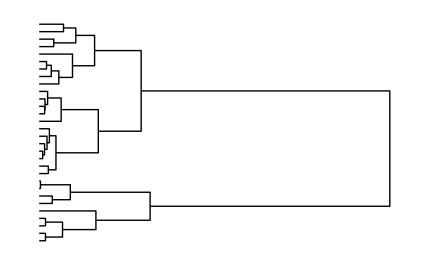

```mathematica
de=DendrogramPlot[caroteDataT->caroteDataID,Linkage->"Ward",DistanceFunction->EuclideanDistance,Orientation->Right]
```

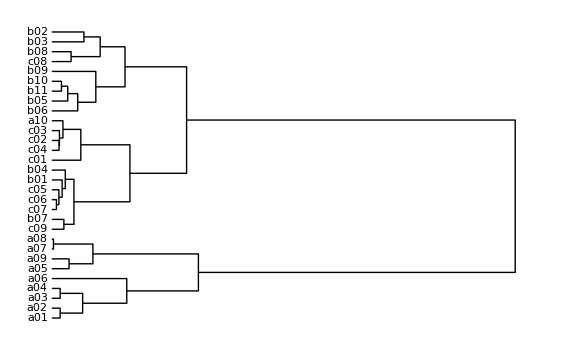

```mathematica
de2=DendrogramPlot[caroteDataT->caroteDataID,Linkage->"Ward",DistanceFunction->EuclideanDistance,Orientation->Right,LeafLabels->caroteDataID]
```

```mathematica
(clsp=Table[ClusterSplit[cl,n],{n,Length[caroteDataID]}])//Short
```

{{«1»},«28»,{a01,a02,a03,a04,a06,«20»,b09,c08,b08,b03,b02}}

```mathematica
clf=Map[ClusterFlatten,clsp,{2}]/.ClusterFlatten->List;
```

```mathematica
Map[Length[#]&,clf]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
Map[Length[#//Flatten]&,clf]
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

## 評価

```mathematica
clfN=clf/.cIDtoNo;
```

### CVI評価:

piS

```mathematica
clfE=Table[piS[caroteDataT,clfN[[n]]],{n,Length[clfN]}]//N
```

{30.,89.0079,86.5379,193.747,216.827,158.641,204.411,169.754,142.05,111.496,88.1905,75.464,67.121,60.0117,61.4333,53.7554,47.8462,43.9555,42.6964,39.7014,38.5812,37.6512,35.6424,34.1326,32.6475,31.8017,30.662,29.8734,29.4994,30.}

```mathematica
Position[clfE,Min[clfE]]
```

{{29}}

piG

```mathematica
clfE=Table[piG[caroteDataT,clfN[[n]]],{n,Length[clfN]}]//N
```

{30.,13.3423,9.2006,10.5525,10.6267,10.3561,11.3355,11.7201,12.2286,12.727,13.2916,13.9871,14.7497,15.5338,16.4783,17.2589,18.0669,18.9153,19.8272,20.6975,21.6171,22.5439,23.4422,24.3548,25.2683,26.2022,27.1275,28.0648,29.0171,30.}

```mathematica
Position[clfE,Min[clfE]]
```

{{3}}

```mathematica
clf[[3]]
```

{{a01,a02,a03,a04,a06},{a05,a09,a07,a08},{c09,b07,c07,c06,c05,b01,b04,c01,c04,c02,c03,a10,b06,b05,b11,b10,b09,c08,b08,b03,b02}}

piSIM

```mathematica
clfE2=Table[piSIM[csimd,clfN[[n]]],{n,Length[clfN]}]//N
```

{30.,360.46,1173.57,7847.58,28011.8,26848.5,68439.,77750.1,69949.6,77525.3,43016.4,46876.,40713.,32997.5,50168.6,27058.7,14541.4,10329.4,8752.78,4660.31,3687.05,2910.73,1539.41,812.708,428.337,299.011,157.107,109.363,57.3116,30.}

```mathematica
Position[clfE2,Min[clfE2]]
```

{{1}}

piSIMG

```mathematica
clfE3=Table[piSIMG[csimd,clfN[[n]]],{n,Length[clfN]}]//N
```

{30.,26.85,21.9407,26.6213,28.096,24.3564,26.0092,25.2082,24.3515,24.4875,23.3324,23.9054,24.1463,24.3787,25.766,25.4614,25.2888,25.6176,26.2381,26.2663,26.8595,27.47,27.6123,27.7939,28.0088,28.5608,28.8198,29.3962,29.6893,30.}

```mathematica
Position[clfE3,Min[clfE3]]
```

{{3}}

cls[[3]] が適正

```mathematica
clf[[3]]
```

{{a01,a02,a03,a04,a06},{a05,a09,a07,a08},{c09,b07,c07,c06,c05,b01,b04,c01,c04,c02,c03,a10,b06,b05,b11,b10,b09,c08,b08,b03,b02}}

# 発表用:

```mathematica
cl
```

Cluster[Cluster[Cluster[Cluster[Cluster[a01,a02,9.13928,1,1],Cluster[a03,a04,9.19687,1,1],33.9248,2,2],a06,82.422,4,1],Cluster[Cluster[a05,a09,18.9713,1,1],Cluster[a07,a08,1.8294,1,1],45.1898,2,2],161.177,5,4],Cluster[Cluster[Cluster[Cluster[c09,b07,13.2869,1,1],Cluster[Cluster[Cluster[Cluster[c07,c06,5.1093,1,1],c05,7.80542,2,1],b01,11.3643,3,1],b04,14.8376,4,1],24.3593,2,5],Cluster[c01,Cluster[Cluster[Cluster[c04,c02,7.95359,1,1],c03,8.40292,2,1],a10,12.2278,3,1],31.9108,1,4],85.8904,7,5],Cluster[Cluster[Cluster[b06,Cluster[b05,Cluster[b11,b10,10.6365,1,1],17.5202,1,2],28.5092,1,3],b09,48.393,4,1],Cluster[Cluster[c08,b08,21.218,1,1],Cluster[b03,b02,35.333,1,1],53.1813,2,2],80.4979,5,4],148.185,12,9],509.439,9,21]

```mathematica
cl[[3]]
```

509.439

```mathematica
Cases[cl,Cluster[_,_,_,_,_],{0,Infinity}]//Length
```

29

```mathematica
lvDist=Sort[Map[#[[3]]&,Cases[cl,Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&]
```

{509.439,161.177,148.185,85.8904,82.422,80.4979,53.1813,48.393,45.1898,35.333,33.9248,31.9108,28.5092,24.3593,21.218,18.9713,17.5202,14.8376,13.2869,12.2278,11.3643,10.6365,9.19687,9.13928,8.40292,7.95359,7.80542,5.1093,1.8294}

```mathematica
lvDistZ=Append[lvDist,0]
```

{509.439,161.177,148.185,85.8904,82.422,80.4979,53.1813,48.393,45.1898,35.333,33.9248,31.9108,28.5092,24.3593,21.218,18.9713,17.5202,14.8376,13.2869,12.2278,11.3643,10.6365,9.19687,9.13928,8.40292,7.95359,7.80542,5.1093,1.8294,0}

```mathematica
clfE
```

{30.,13.3423,9.2006,10.5525,10.6267,10.3561,11.3355,11.7201,12.2286,12.727,13.2916,13.9871,14.7497,15.5338,16.4783,17.2589,18.0669,18.9153,19.8272,20.6975,21.6171,22.5439,23.4422,24.3548,25.2683,26.2022,27.1275,28.0648,29.0171,30.}

```mathematica
lvPoints=Transpose[{lvDistZ,clfE}]
```

{{509.439,30.},{161.177,13.3423},{148.185,9.2006},{85.8904,10.5525},{82.422,10.6267},{80.4979,10.3561},{53.1813,11.3355},{48.393,11.7201},{45.1898,12.2286},{35.333,12.727},{33.9248,13.2916},{31.9108,13.9871},{28.5092,14.7497},{24.3593,15.5338},{21.218,16.4783},{18.9713,17.2589},{17.5202,18.0669},{14.8376,18.9153},{13.2869,19.8272},{12.2278,20.6975},{11.3643,21.6171},{10.6365,22.5439},{9.19687,23.4422},{9.13928,24.3548},{8.40292,25.2683},{7.95359,26.2022},{7.80542,27.1275},{5.1093,28.0648},{1.8294,29.0171},{0,30.}}

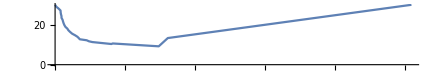

```mathematica
pl=ListPlot[lvPoints,Joined->True,PlotRange->All,AspectRatio->1/6]
```

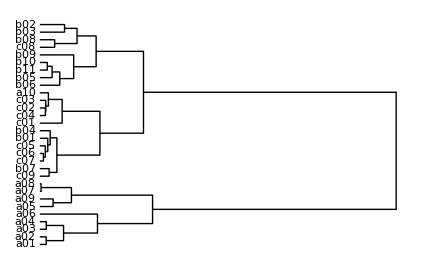

```mathematica
de2
```

## Exam

```mathematica
ra=Table[RandomReal[],{8},{5}]
```

```mathematica
dmat=Outer[EuclideanDistance,ra,ra,1]
```

```mathematica
st={{1,0,0,0},{1,0,0,0},{0,1,0,0},{0,1,0,0},{0,0,1,0},{0,0,1,0},{0,0,0,1},{0,0,0,1}}
```

```mathematica
dmats=Outer[EuclideanDistance,st,st//N,1]
```

```mathematica
piDMG[dmats,{{1,2},{3,4},{5,6},{7,8}}]
```